# Heaviside Bifurcation

## Import XPP/Auto Data

```mathematica
infile = (*<infile from 01_proces.m>*);
outfile = (*<outfile>*);

points=infile;
mat=Import[points];
size=Dimensions[mat];
M=size[[1]];
mat2=ArrayFlatten[{{mat,0}}]; (*add a binary column to test results*)
```

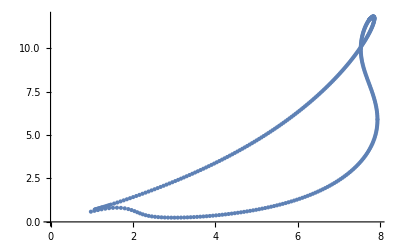

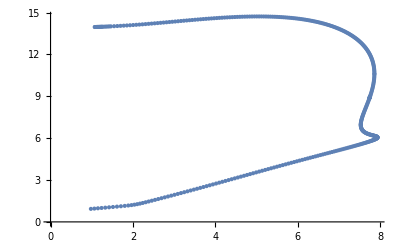

```mathematica
(*plot bifurcation diagrams for consistency*)
X=mat[[All,1]];
Y=mat[[All,2]];
Z = mat[[All,3]];
T1=Transpose@{X,Y};
ListPlot[T1]
T2=Transpose@{X,Z};
ListPlot[T2]
```

## Parameters

```mathematica
x0=7.75;h=2.7;
A=3;B=1.5;
AA=2.7;BB=0;
a=0.42;aa=.43;b=0.11;bb=b;
c=aa;
V=8;TH=10; (*stable bump*)
(*V=12;TH=8;*)
tol=10^(-12);
```

## Compute Bifurcation Points

```mathematica
(*loop over all values of x0*)
For[i=1,i≤M,i++,
x0=mat[[i,1]];
V=mat[[i,2]];
TH=mat[[i,3]];

(*v and theta dependent values*)
A0=A/a;B0=B/b;
A1[v_]:=A/(a*(a-1/v));
B1[v_]:=B/(b*(b-1/v));
A2[v_]:=A/(a*(a+1/v));
B2[v_]:=B/(b*(b+1/v));
AA0=AA/aa;BB0=BB/bb;
AA1[v_]:=AA/(aa*(aa-1/v));
BB1[v_]:=BB/(bb*(bb-1/v));
AA2[v_]:=AA/(aa*(aa+1/v));
BB2[v_]:=BB/(bb*(bb+1/v));
a1[theta_]:=1-Exp[a*theta];
b1[theta_]:=1-Exp[b*theta];
aa1[theta_]:=Exp[aa*x0]-Exp[aa*(theta+x0)];
bb1[theta_]:=Exp[bb*x0]-Exp[bb*(theta+x0)];

(*solve heaviside system to get exact coordinates*)
F=h-(1/v)*
(
2*(1-Exp[-theta/v])*v*(A0-B0+Exp[-x0/v]*(AA0-BB0))+
A1[v]*(Exp[-a*theta]-Exp[-theta/v])-
B1[v]*(Exp[-b*theta]-Exp[-theta/v])+
AA1[v]*(Exp[-aa*x0]*(Exp[-aa*theta]-1)+Exp[-x0/v]*(1-Exp[-theta/v]))-
BB1[v]*(Exp[-bb*x0]*(Exp[-bb*theta]-1)+Exp[-x0/v]*(1-Exp[-theta/v]))+
(Exp[-theta/v]-1)*(A2[v]-B2[v]+Exp[-x0/v]*(AA2[v]-BB2[v]))
);

G=-h+Exp[theta/v]*
(
h-(1/v)*
(
2*v*((A0-B0)*(1-Exp[-theta/v])+(AA0-BB0)*(Exp[-x0/v]-Exp[-theta/v]))+
A1[v]*(Exp[-a*theta]-Exp[-theta/v])-
B1[v]*(Exp[-b*theta]-Exp[-theta/v])+
AA1[v]*(Exp[-x0/v]-Exp[-aa*x0]*(1+Exp[-theta/v]-Exp[-aa*theta]))-
BB1[v]*(Exp[-x0/v]-Exp[-bb*x0]*(1+Exp[-theta/v]-Exp[-bb*theta]))+
A2[v]*(Exp[-theta*(a+1/v)]-1)-
B2[v]*(Exp[-theta*(b+1/v)]-1)+
AA2[v]*(Exp[aa*x0]*Exp[-theta*(aa+1/v)]-Exp[-x0/v])-
BB2[v]*(Exp[bb*x0]*Exp[-theta*(bb+1/v)]-Exp[-x0/v])
)
);

sol=SetPrecision[ FindRoot[{F==0,G==0},{v,V},{theta,TH}],30];
vv=v/.sol[[1]];
th=theta/.sol[[2]];
mat2[[i,2]]=vv;
mat2[[i,3]]=th;

(*construct solution at coordinates*)
integral1[x_]:=
A1[vv]*(1-Exp[-a*th])*(Exp[x*(a-1/vv)]-1)-B1[vv]*(1-Exp[-b*th])*(Exp[x*(b-1/vv)]-1)+
AA1[vv]*Exp[-aa*x0]*(1-Exp[-aa*th])*(Exp[x*(aa-1/vv)]-1)-
BB1[vv]*Exp[-bb*x0]*(1-Exp[-bb*th])*(Exp[x*(bb-1/vv)]-1);
integral2[x_]:=
2*(A0-B0)*vv*(1-Exp[-x/vv])+
A1[vv]*Exp[-a*th]*(1-Exp[x*(a-1/vv)])-
B1[vv]*Exp[-b*th]*(1-Exp[x*(b-1/vv)])+
AA1[vv]*Exp[-aa*x0]*(Exp[-aa*th]-1)*(1-Exp[x*(aa-1/vv)])-
BB1[vv]*Exp[-bb*x0]*(Exp[-bb*th]-1)*(1-Exp[x*(bb-1/vv)])+
A2[vv]*(Exp[-x*(a+1/vv)]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]-1);
integral3a[x_]:=
2*(A0-B0)*vv*(1-Exp[-x/vv])+
2*(AA0-BB0)*vv*(Exp[-x0/vv]-Exp[-x/vv])+
A1[vv]*Exp[-a*th]*(1-Exp[x*(a-1/vv)])-
B1[vv]*Exp[-b*th]*(1-Exp[x*(b-1/vv)])+
AA1[vv]*(Exp[-aa*(th+x0)]*(1-Exp[x*(aa-1/vv)])+Exp[-x0/vv]-Exp[-aa*x0])-
BB1[vv]*(Exp[-bb*(th+x0)]*(1-Exp[x*(bb-1/vv)])+Exp[-x0/vv]-Exp[-bb*x0])+
A2[vv]*(Exp[-x*(a+1/vv)]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]-1)+
AA2[vv]*(Exp[aa*x0]*Exp[-x*(aa+1/vv)]-Exp[-x0/vv])-
BB2[vv]*(Exp[bb*x0]*Exp[-x*(bb+1/vv)]-Exp[-x0/vv]);
integral3b[x_]:=
2*(A0-B0)*vv*(1-Exp[-th/vv])+
A1[vv]*(Exp[-a*th]-Exp[-th/vv])-
B1[vv]*(Exp[-b*th]-Exp[-th/vv])+
AA1[vv]*Exp[-aa*x0]*(Exp[-aa*th]-1)*(1-Exp[x*(aa-1/vv)])-
BB1[vv]*Exp[-bb*x0]*(Exp[-bb*th]-1)*(1-Exp[x*(bb-1/vv)])+
A2[vv]*(Exp[-x*(a+1/vv)]*(1-Exp[a*th])+Exp[-th/vv]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]*(1-Exp[b*th])+Exp[-th/vv]-1);
integral3[x_]:=If[x0<th,integral3a[x],integral3b[x]];
integral4[x_]:=
2*(A0-B0)*vv*(1-Exp[-th/vv])+
2*(AA0-BB0)*vv*(Exp[-x0/vv]-Exp[-x/vv])+
A1[vv]*(Exp[-a*th]-Exp[-th/vv])-
B1[vv]*(Exp[-b*th]-Exp[-th/vv])+
AA1[vv]*(Exp[-aa*(th+x0)]*(1-Exp[x*(aa-1/vv)])+Exp[-x0/vv]-Exp[-aa*x0])-
BB1[vv]*(Exp[-bb*(th+x0)]*(1-Exp[x*(bb-1/vv)])+Exp[-x0/vv]-Exp[-bb*x0])+
A2[vv]*(Exp[-x*(a+1/vv)]*(1-Exp[a*th])+Exp[-th/vv]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]*(1-Exp[b*th])+Exp[-th/vv]-1)+
AA2[vv]*(Exp[aa*x0]*Exp[-x*(aa+1/vv)]-Exp[-x0/vv])-
BB2[vv]*(Exp[bb*x0]*Exp[-x*(bb+1/vv)]-Exp[-x0/vv]);
integral5[x_]:=
2*(A0-B0)*vv*(1-Exp[-th/vv])+
2*(AA0-BB0)*vv*(Exp[-x0/vv]-Exp[-(th+x0)/vv])+
A1[vv]*(Exp[-a*th]-Exp[-th/vv])-
B1[vv]*(Exp[-b*th]-Exp[-th/vv])+
AA1[vv]*(Exp[-x0/vv]*(1-Exp[-th/vv])-Exp[-aa*x0]*(1-Exp[-aa*th]))-
BB1[vv]*(Exp[-x0/vv]*(1-Exp[-th/vv])-Exp[-bb*x0]*(1-Exp[-bb*th]))+
A2[vv]*(Exp[-x*(a+1/vv)]*(1-Exp[a*th])+Exp[-th/vv]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]*(1-Exp[b*th])+Exp[-th/vv]-1)+
AA2[vv]*(Exp[-x*(aa+1/vv)]*(Exp[aa*x0]-Exp[aa*(th+x0)])+Exp[-(th+x0)/vv]-Exp[-x0/vv])-
BB2[vv]*(Exp[-x*(bb+1/vv)]*(Exp[bb*x0]-Exp[bb*(th+x0)])+Exp[-(th+x0)/vv]-Exp[-x0/vv]);
curve1[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral1[x];
curve2[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral2[x];
curve3[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral3[x];
curve4[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral4[x];
curve5[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral5[x];
u5[x_]:=-(1/vv)*(a1[th]*A2[vv]*Exp[-x*a]-b1[th]*B2[vv]*Exp[-x*b]+aa1[th]*AA2[vv]*Exp[-x*aa]-bb1[th]*BB2[vv]*Exp[-x*bb]);

travbump[x_]:=Piecewise[{
{curve1[x],x<=0},
{curve2[x],0<x<=Min[x0,th]},
{curve3[x],Min[x0,th]<x<=Max[x0,th]},{curve4[x],Max[x0,th]<x<=x0+th},
(*{curve5[x],x0+th<x<Infinity}*)
{u5[x],x0+th<x<Infinity}
}];
l=Abs[travbump[0]-h];
r=Abs[travbump[th]-h];

(*mark binary column 1 if solution error is within specified tolerance*)
If[
l<=tol && r<=tol && curve1[0]-curve2[0]<=tol && curve2[x0]-curve3[x0]<=tol && curve3[th]-curve4[th]<=tol && curve4[x0+th]-curve5[x0+th]<=tol
,mat2[[i,4]]=1]
]

(*export tested bifurcation solutions*)
Export[outfile,mat2];
mat//MatrixForm;
mat2 // MatrixForm;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

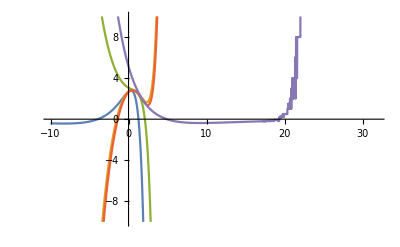

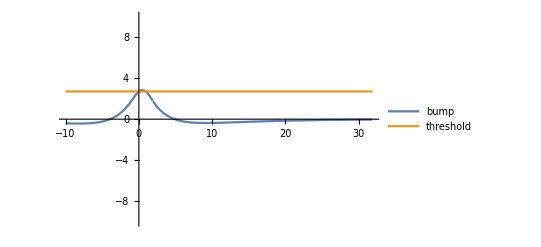

```mathematica
(*Plot solution*)
Plot[{curve1[x],curve2[x],curve3[x],curve4[x],curve5[x]},{x,-10,x0+th+30},PlotRange->10]
Plot[{travbump[x],h},{x,-10,x0+th+30},PlotLegends->{"bump","threshold"},PlotRange->10]
```

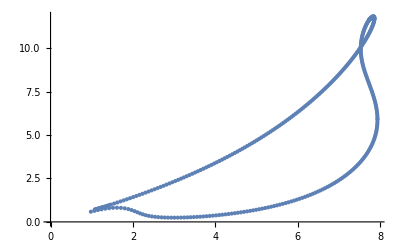

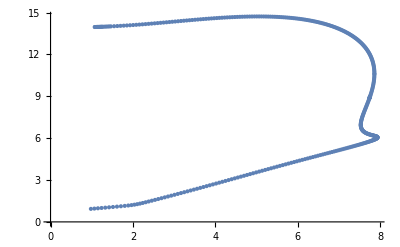

```mathematica
(*double check bifurcation diagrams at solution coordinates for consistency*)
X2=mat2[[All,1]];
Y2=mat2[[All,2]];
Z2=mat2[[All,3]];
S1=Transpose@{X2,Y2};
ListPlot[S1]
S2=Transpose@{X2,Z2};
ListPlot[S2]
```